```mathematica
Import["
```

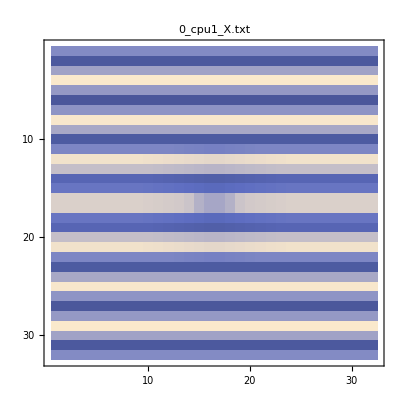
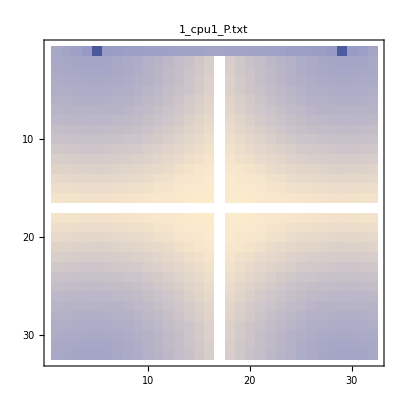
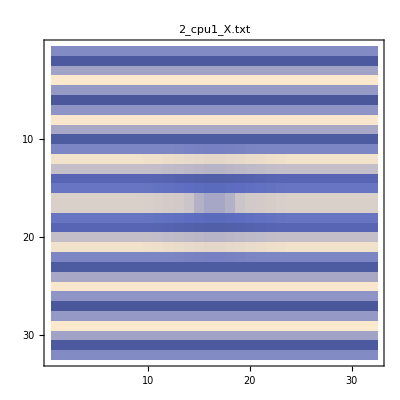
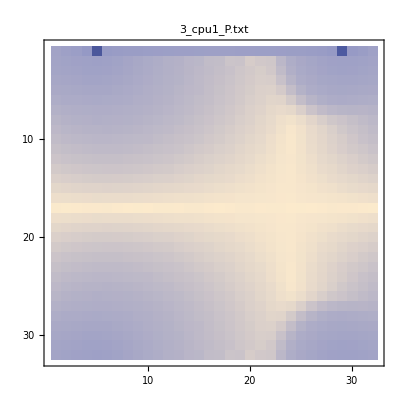
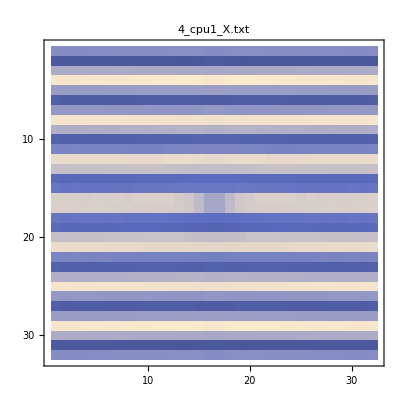
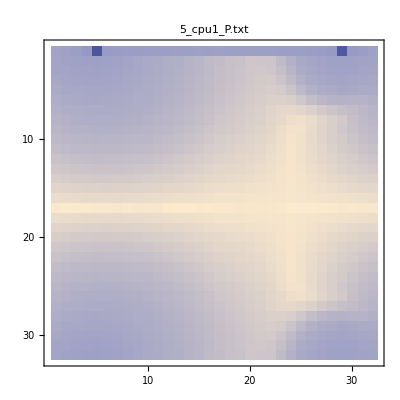
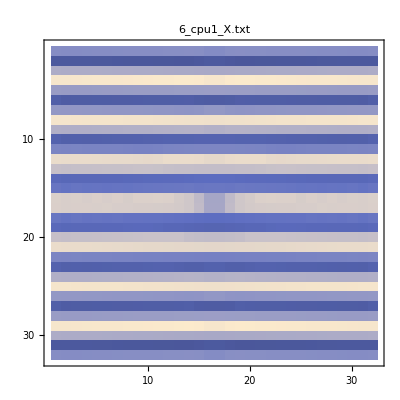
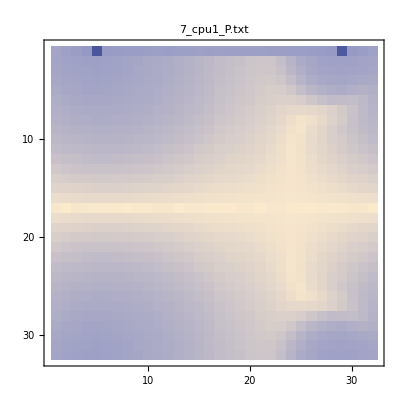
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
names=FileNames["/Users/ranza/Projects/Quantum/QSF-examples/template/Results/*.txt"];
Multicolumn[ MatrixPlot[Partition[Import[#,"CSV"][[All,3]],32],PlotLabel->FileNameTake[#],PlotTheme->"Scientific"]&/@names,4,Appearance->"Horizontal"]
```

```mathematica
DoubleQ[size_]:=size==8;
ReadBinaryWFHeader[st_]:=Join[BinaryReadList[st, "Integer32",3],BinaryReadList[st, "Real64",3]];
ReadBinaryWF[st_,dim_,n_,size_]:=Block[{typesize=If[DoubleQ[size],"Real64","Complex128"]},
Apply[Table[BinaryReadList[st, typesize,n],##]&,ConstantArray[n,dim-1]]
];
ImportBinaryAndPlot[file_,collapse_:False,scaleF_:Identity,opts___]:=Block[{dim,n,size,min,max,delta,st,
norm,dat,base,opt,rng,vLabel,ψ},
(*read*)
st=OpenRead[file,BinaryFormat->True];
{dim,n,size,min,max,delta}=ReadBinaryWFHeader[st];
dat=ReadBinaryWF[st,dim,n,size];
Close[file];

base=FileNameTake[file];
rng={min,max};

vLabel=Style[#,FontFamily->"Latin Modern Roman",14]&/@If[DoubleQ[size],(|ψ|)^2, {Abs[ψ],Arg[ψ]}];

dat=If[collapse,Abs[dat]^2,dat];
norm=Total[dat,∞];

dat=scaleF@dat;
Switch[dim,
1,If[DoubleQ[size]|| collapse,
Prob1D[dat,rng,opts],
GRID[{{Prob1D[Abs[dat]^2,rng,250,PlotStyle->Black],Phase1D[Arg@dat,rng,250,FrameStyle->Red,PlotStyle->Red]}}]],
2,If[DoubleQ[size]|| collapse,
Prob2D[dat,rng,norm,opts],
GRID[{{Prob2D[Abs[dat]^2,rng,250,True]},{Phase2D[Arg@dat,rng,250]}}]],
3,If[ DoubleQ[size]|| collapse,
Prob3D[dat,rng,norm,opts],
GRID[{{Prob3D[Abs[dat]^2,rng,250]},{Phase3D[Arg@dat,rng,250]}}]]
]
];
ImportBinaryWF[file_,collapse_:False]:=Block[{dim,n,size,min,max,delta,st,
norm,dat,base,opt,rng,vLabel,ψ},
(*read*)
st=OpenRead[file,BinaryFormat->True];
{dim,n,size,min,max,delta}=ReadBinaryWFHeader[st];
dat=ReadBinaryWF[st,dim,n,size];
dat=If[collapse,Abs[dat]^2,dat];
Close[file];
dat
];
```